## VerticesOnBoundary-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.0 (11-Nov-2012)) loaded Sun 11 Nov 2012 19:31:24
using xCellerator 0.92 and XSSA 1204002
GPL License Terms Apply

There are 8 cells in the tissue.

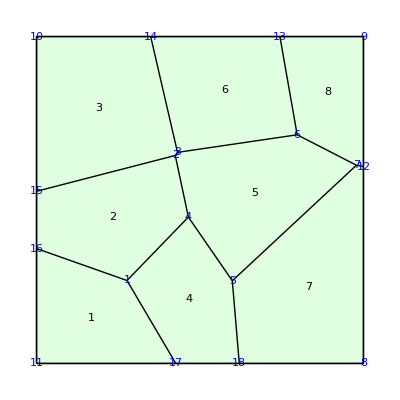

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Print["There are ", NTissueCells[q], " cells in the tissue."];  
ShowTissue[q, "CellNumbers"-> True, "VertexNumbers"-> {Blue,FontSize-> 18}]
```

```mathematica
VerticesOnBoundary[q]
```

{8,12,9,13,14,10,15,16,11,17,18}

```mathematica
VerticesNotOnBoundary[q]
```

{1,2,3,4,5,6,7}